```mathematica
Subscript[Ω, 1] = 14;
Subscript[Ω, 2] = 1.4;
Subscript[Δ, d] = 200;
Subscript[Δ, p] = 207.24;
δ = 7;
H1 = {{0, Subscript[Ω, 1]/2,  Subscript[Ω, 1]/2},{Subscript[Ω, 1]/2, Subscript[Δ, d]+δ, 0},
{Subscript[Ω, 1]/2, 0, Subscript[Δ, d]-δ}};
H2 = {{0, Subscript[Ω, 1]/2,- Subscript[Ω, 2]/2,  Subscript[Ω, 1]/2},{Subscript[Ω, 1]/2, Subscript[Δ, d]+δ, 0 , 0},
{- Subscript[Ω, 2]/2, 0, Subscript[Δ, p], 0},{Subscript[Ω, 1]/2, 0,0, Subscript[Δ, d]-δ}};
```

```mathematica
N[Eigensystem[H1]]
```

{{207.24,193.249,-0.4894},{{2.03435,59.2284,1.},{0.0355669,-0.0181054,1.},{-27.6413,0.932527,1.}}}

```mathematica
N[Eigensystem[H2]]
```

{{207.265,207.217,193.249,-0.491754},{{-0.0262388,-0.691899,0.721403,-0.0128753},{-0.0223884,-0.720981,-0.692506,-0.0110231},{0.0355322,-0.0180877,0.00177774,0.999203},{-0.998773,0.0336949,-0.0033656,0.0361329}}}

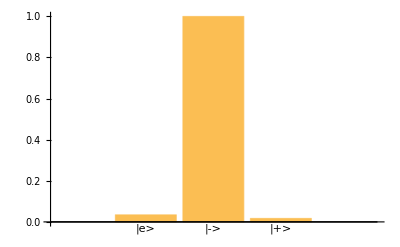

```mathematica
BarChart[{0.0343,0.9993,0.0169},ChartLabels->{"|e>","|->","|+>"}]
```

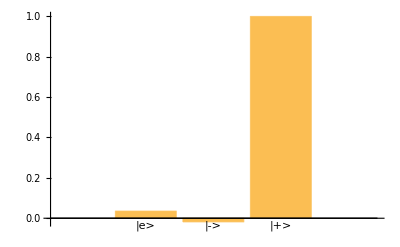

```mathematica
BarChart[{0.0355,-0.0181,0.9992},ChartLabels->{"|e>","|->","|+>"}]
```

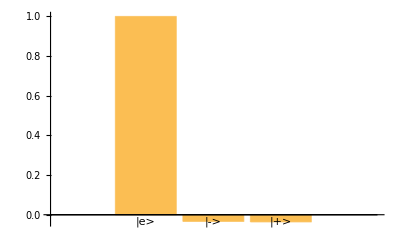

```mathematica
BarChart[{0.9988,-0.0337,-0.0361},ChartLabels->{"|e>","|->","|+>"}]
```